```mathematica
(* This is to get the SSM potential between Ca and Cl*)
```

```mathematica
(* The main task is to get v_{R1,Ca Water} , v_{R1, Cl Water} and  v_{R1,Ca Cl}. I will denote it by fvR1CaA, fvR1ClA and fvR1CaCl respectively *)
```

```mathematica
(* This handling of the surface charge is a bit tricky. Maybe use a smoothed charge will make the analysis easier. I can just use the delta charge for now *)
(* when a surface charge of Q is convoluted with a potention ϕ. The 
 result is NIntegrate[Q/2 ϕ[Sqrt[rqcut^2+r^2-2 r rqcut x]],{x,-1,1}], where rqcut is the position of the surface charge *)
```

```mathematica
(* The screening charge around ion Ca is denoted by frhoqCa for the full system and frhoqCa0 for the GT system. Definition is similar for the Cl *)
```

```mathematica
Quit[]
```

```mathematica
ϵ=71
```

71

```mathematica
Qna=1
Qnashield=-Qna (1 -1/ϵ)
```

1

-70/71

```mathematica
Qcl=-1
Qclshield=-Qcl(1 -1/ϵ)
```

-1

70/71

```mathematica
d=0.2
ss=6
fintqcorrect[r_]:=Piecewise[{{0, r<d}, {Erf[(r-d)/ss], r≥d}}]
frhoqcorrect[r_]:=Piecewise[{{0, r<d}, {fintqcorrect'[r]/(4π r^2), r≥d}}]
```

0.2

6

```mathematica
(* frhoqCa0=frhoqCa-Qcashield frhoqcorrect, without considering the surface charge, total surface charge is Qcashield-Qcacut *)
```

```mathematica
rrhoqNa=Import["/Users/anggao/Desktop/Na_Ca_Cl_potentials/rhoq_Na_full.txt","Table"];
```

```mathematica
frhoqNa=Interpolation[rrhoqNa]
```

InterpolatingFunction[{{0.001,1.999}},<>]

```mathematica
rrhoqCl=Import["/Users/anggao/Desktop/Na_Ca_Cl_potentials/rhoq_Cl_full.txt","Table"];
```

```mathematica
frhoqCl=Interpolation[rrhoqCl]
```

InterpolatingFunction[{{0.001,1.999}},<>]

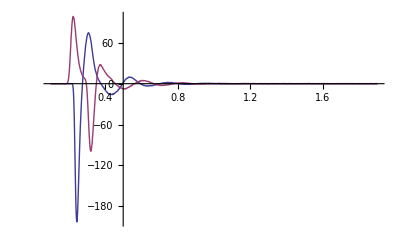

```mathematica
Plot[{frhoqNa[r],frhoqCl[r]},{r,0.1,1.9},PlotRange->Full]
```

```mathematica
frhoqNa0[r_]:=frhoqNa[r]-Qnashield frhoqcorrect[r]
```

```mathematica
frhoqCl0[r_]:=frhoqCl[r]-Qclshield frhoqcorrect[r]
```

```mathematica
rqcut=1.99
```

1.99

```mathematica
Qnacut=NIntegrate[frhoqNa[rp] 4 π rp^2,{rp,0,rqcut}]
```

-1.01304

```mathematica
Qnacut-Qnashield
```

-0.0271201

```mathematica
Qclcut=NIntegrate[frhoqCl[rp] 4 π rp^2,{rp,0,rqcut}]
```

0.962526

```mathematica
Qclcut-Qclshield
```

-0.0233893

```mathematica
fG[r_,rp_,s_]:=1/(2 r rp)(Abs[r+rp] Erf[Abs[r+rp]/s] + s/Sqrt[π] Exp[-(Abs[r+rp]/s)^2] 
            - Abs[r-rp]Erf[Abs[r-rp]/s] - s/Sqrt[π] Exp[-(Abs[r-rp]/s)^2] )
```

```mathematica
rhosurf[r_,rcut_]:=DiracDelta[r-rcut]/(4 π rcut^2)
```

```mathematica
fVR1surf[r_,rcut_]:=1/(2 r rcut)(-0.28209479177387814 ⅇ^(-4. Abs[r-rcut]^2)+0.28209479177387814 ⅇ^(-4. Abs[r+rcut]^2)-Abs[r-rcut] Erf[2. Abs[r-rcut]]+Abs[r+rcut] Erf[2. Abs[r+rcut]])
```

```mathematica
(* to get fVR1surf, we already assumed that the smoothed length sigma=0.5 *)
```

```mathematica
(* Calculate fVR1CaA first *)
```

```mathematica
s=0.5 (* the sigma parameter for v1 *)
```

0.5

```mathematica
frenormNaA[r_?NumericQ]:=NIntegrate[frhoqNa[rp]fG[r,rp,s]4π rp^2,{rp,0.01,rqcut}]+(Qnashield-Qnacut) fVR1surf[r,rqcut]
```

```mathematica
tableVrenormNaA=ParallelTable[frenormNaA[r],{r,0.01,4.91,0.05}]
```

{-2.17834,-2.16869,-2.14557,-2.10976,-2.06242,-2.00504,-1.93933,-1.86713,-1.79032,-1.71071,-1.62999,-1.54964,-1.47091,-1.39479,-1.32204,-1.25318,-1.1885,-1.12813,-1.07206,-1.02016,-0.972225,-0.928013,-0.887245,-0.849636,-0.814906,-0.782787,-0.75303,-0.725406,-0.699708,-0.67575,-0.653368,-0.632413,-0.612755,-0.594278,-0.57688,-0.560469,-0.544964,-0.530292,-0.516388,-0.503193,-0.490656,-0.478727,-0.467365,-0.456531,-0.446188,-0.436304,-0.426849,-0.417797,-0.409121,-0.400799,-0.39281,-0.385135,-0.377754,-0.370651,-0.36381,-0.357219,-0.350861,-0.344727,-0.338803,-0.33308,-0.327547,-0.322195,-0.317015,-0.311999,-0.307139,-0.302428,-0.29786,-0.293427,-0.289125,-0.284947,-0.280888,-0.276943,-0.273107,-0.269376,-0.265745,-0.262212,-0.25877,-0.255419,-0.252152,-0.248969,-0.245864,-0.242836,-0.239882,-0.236999,-0.234184,-0.231436,-0.228751,-0.226127,-0.223564,-0.221057,-0.218607,-0.21621,-0.213865,-0.21157,-0.209324,-0.207125,-0.204972,-0.202863,-0.200797}

```mathematica
interpVrenormNaA=Interpolation[Transpose[{Table[r,{r,0.01,4.91,0.05}],tableVrenormNaA}]]
```

InterpolatingFunction[{{0.01,4.91}},<>]

```mathematica
fVR1NaA[r_]:=Piecewise[{{interpVrenormNaA[r]+Qna Erf[r/s]/r, r<4.5}, {Qna/(ϵ r), r≥ 4.5}}]
```

```mathematica
fvR1NaA[r_]:=fVR1NaA[r]/Qna
```

InterpolatingFunction::dmval: Input value {0.000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

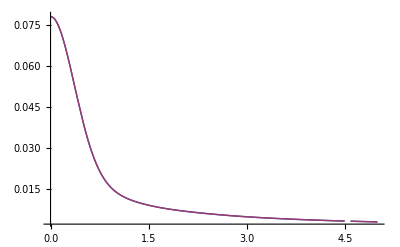

```mathematica
Plot[{fVR1NaA[r],fvR1NaA[r]},{r,0,5},PlotRange->Full]
```

```mathematica
(* successfully obtained fvR1CaA *)
```

```mathematica
fvR1NaA[0.5]
```

0.0392474

```mathematica
frenormClA[r_?NumericQ]:=NIntegrate[frhoqCl[rp]fG[r,rp,s]4π rp^2,{rp,0.01,rqcut}]+(Qclshield-Qclcut) fVR1surf[r,rqcut]
```

```mathematica
tableVrenormClA=ParallelTable[frenormClA[r],{r,0.01,4.91,0.05}]
```

{2.16426,2.15475,2.13198,2.0967,2.05005,1.99349,1.92869,1.85748,1.78168,1.70309,1.62334,1.54392,1.46603,1.39068,1.3186,1.25032,1.18613,1.12616,1.07042,1.01878,0.97105,0.926994,0.886344,0.848825,0.814161,0.782093,0.752376,0.724785,0.699116,0.675187,0.652832,0.631905,0.612277,0.593833,0.576468,0.560091,0.544621,0.529984,0.516115,0.502954,0.490448,0.47855,0.467215,0.456406,0.446085,0.436221,0.426783,0.417744,0.409081,0.400769,0.392787,0.385117,0.377741,0.370642,0.363804,0.357214,0.350859,0.344725,0.338802,0.333079,0.327546,0.322194,0.317015,0.311999,0.307139,0.302428,0.29786,0.293427,0.289125,0.284947,0.280888,0.276943,0.273107,0.269376,0.265745,0.262212,0.25877,0.255419,0.252152,0.248969,0.245864,0.242836,0.239882,0.236999,0.234184,0.231436,0.228751,0.226127,0.223564,0.221057,0.218607,0.21621,0.213865,0.21157,0.209324,0.207125,0.204972,0.202863,0.200797}

```mathematica
interpVrenormClA=Interpolation[Transpose[{Table[r,{r,0.01,4.91,0.05}],tableVrenormClA}]]
```

InterpolatingFunction[{{0.01,4.91}},<>]

```mathematica
fVR1ClA[r_]:=Piecewise[{{interpVrenormClA[r]+Qcl Erf[r/s]/r, r<4.5}, {Qcl/(ϵ r), r≥ 4.5}}]
```

```mathematica
fvR1ClA[r_]:=fVR1ClA[r]/Qcl
```

InterpolatingFunction::dmval: Input value {0.0000921329} lies outside the range of data in the interpolating function. Extrapolation will be used.

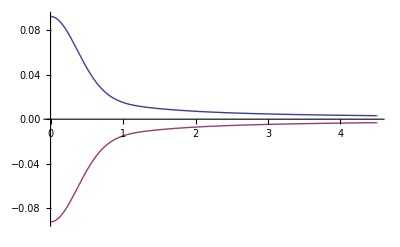

```mathematica
Plot[{fvR1ClA[r],fVR1ClA[r]},{r,0,4.51},PlotRange->Full]
```

```mathematica
frenormNaCl[r_?NumericQ]:=-1/Qna(NIntegrate[2 π rp^2 frhoqNa[rp] (fvR1ClA[Sqrt[rp^2+r^2-2 r rp x]]-Erf[Sqrt[rp^2+r^2-2 r rp x]/s]/Sqrt[rp^2+r^2-2 r rp x]),{rp, 0.01, rqcut},{x,-1,1}]+ NIntegrate[(Qnashield-Qnacut)/2 (fvR1ClA[Sqrt[rqcut^2+r^2-2 r rqcut x]]-Erf[Sqrt[rqcut^2+r^2-2 r rqcut x]/s]/Sqrt[rqcut^2+r^2-2 r rqcut x]),{x,-1,1}])
```

```mathematica
tablerenormNaCl=ParallelTable[frenormNaCl[r],{r,0.005,3,0.05}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.975444 and 1.16303×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.931872 and 1.1017×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.07339 and 1.1031×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.788108 and 9.2715×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.891602 and 1.09123×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.02255 and 0.0000133901 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.758567 and 8.85961×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.731128 and 8.02292×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

{-2.09222,-2.08468,-2.06483,-2.03328,-1.99102,-1.93931,-1.87963,-1.8136,-1.74288,-1.66911,-1.59381,-1.51837,-1.44399,-1.37163,-1.30207,-1.23584,-1.17331,-1.11467,-1.05995,-1.00912,-0.962013,-0.918443,-0.878177,-0.840965,-0.806555,-0.774703,-0.745173,-0.71775,-0.692235,-0.668448,-0.646228,-0.625428,-0.605921,-0.587592,-0.570337,-0.554066,-0.538697,-0.524158,-0.510383,-0.497314,-0.484897,-0.473086,-0.461837,-0.451111,-0.440873,-0.43109,-0.421732,-0.412772,-0.404186,-0.395951,-0.388045,-0.380448,-0.373144,-0.366116,-0.359348,-0.352825,-0.346536,-0.340466,-0.334606,-0.328944}

```mathematica
interprenormNaCl=Interpolation[Transpose[{Table[r,{r,0.005,3,0.05}],tablerenormNaCl}]]
```

InterpolatingFunction[{{0.005,2.955}},<>]

```mathematica
fvR1NaCl[r_]:=Piecewise[{{interprenormNaCl[r]+Erf[r/s]/r, r<2.9}, {2/(ϵ r)-1/(ϵ^2 r), r≥2.9}}]
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

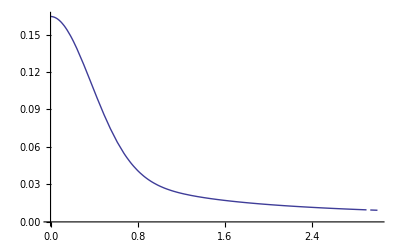

```mathematica
Plot[fvR1NaCl[r],{r,0,3}]
```

```mathematica
(*now calculate vtildeR1CaCl, I will use fvtR1CaCl to denote it.*)
```

```mathematica
fomegaNaCl[r_]:=NIntegrate[2 π rp^2(frhoqNa[rp])Qcl fvR1ClA[Sqrt[rp^2+r^2-2 r rp x]],{rp, 0.01, rqcut},{x,-1,1}]+
1/2 NIntegrate[2 π rp^2(-Qnashield frhoqcorrect[rp])Qcl fvR1ClA[Sqrt[rp^2+r^2-2 r rp x]],{rp, 0.01, 20},{x,-1,1}]+
NIntegrate[(Qnashield-Qnacut)/2 Qcl fvR1ClA[Sqrt[rqcut^2+r^2-2 r rqcut x]],{x,-1,1}]+NIntegrate[2 π rp^2(frhoqCl[rp])Qna fvR1NaA[Sqrt[rp^2+r^2-2 r rp x]],{rp, 0.01, rqcut},{x,-1,1}]+
1/2 NIntegrate[2 π rp^2(-Qclshield frhoqcorrect[rp])Qna fvR1NaA[Sqrt[rp^2+r^2-2 r rp x]],{rp, 0.01,20},{x,-1,1}]+
NIntegrate[(Qclshield-Qclcut)/2 Qna fvR1NaA[Sqrt[rqcut^2+r^2-2 r rqcut x]],{x,-1,1}]
```

```mathematica
tableomegaNaCl=ParallelTable[fomegaNaCl[r],{r,0.005,4,0.05}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0611745 and 2.8821×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0140252 and 3.66448×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0272765 and 3.85471×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0510715 and 2.9316×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0126365 and 3.74713×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.023419 and 3.9201×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0554617 and 1.10576×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0131923 and 2.7844×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0242324 and 6.47901×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0768092 and 9.54671×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0640052 and 9.67735×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0720651 and 1.39886×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0101616 and 6.83653×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00920123 and 4.19266×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00982666 and 5.28351×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00821256 and 1.98607×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00683671 and 3.55171×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00582912 and 3.3181×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00744948 and 1.44502×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00632671 and 6.95853×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00549816 and 5.13292×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00798886 and 1.33093×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00570943 and 3.05153×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00667258 and 6.88394×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.005089 and 3.00926×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0048322 and 3.24013×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00499927 and 2.3225×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00459562 and 9.98108×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00419056 and 5.80165×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00436712 and 1.02728×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00398209 and 5.88628×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00365934 and 3.7706×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00452274 and 3.60119×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00412991 and 5.34211×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{0.148919,0.147577,0.144072,0.138585,0.131393,0.12285,0.113349,0.103291,0.0930658,0.0830219,0.0734467,0.0645591,0.0565059,0.049366,0.0431577,0.0378513,0.033381,0.0296596,0.0265876,0.0240642,0.0219935,0.0202885,0.0188747,0.0176894,0.016682,0.0158127,0.015051,0.0143735,0.0137629,0.0132068,0.012695,0.0122212,0.0117799,0.011367,0.0109795,0.0106149,0.0102711,0.00994637,0.00963902,0.00934778,0.00907137,0.00880864,0.00855868,0.00832044,0.00809321,0.00787601,0.0076684,0.00746972,0.00727944,0.00709708,0.00692224,0.0067545,0.00659355,0.00643903,0.00629071,0.00614809,0.00601113,0.00587947,0.00575286,0.00563107,0.00551384,0.00540098,0.00529226,0.00518748,0.00508645,0.004989,0.00489495,0.00480414,0.00471642,0.00463165,0.00454969,0.00447041,0.0043937,0.00431943,0.00424752,0.00417784,0.00411031,0.00404484,0.00398134,0.00391972}

```mathematica
interpomegaNaCl=Interpolation[Transpose[{Table[r,{r,0.005,4,0.05}],tableomegaNaCl}]]
```

InterpolatingFunction[{{0.005,3.955}},<>]

```mathematica
fvtR1NaCl[r_]:=Piecewise[{{interpomegaNaCl[r]/(Qna Qcl)+fvR1NaCl[r], r<3.9}, {1/(ϵ r), r>=3.9}}]
```

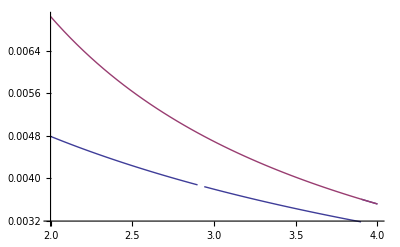

```mathematica
Plot[{fvtR1NaCl[r],1/(ϵ r)},{r,2,4},PlotRange->Full]
```

```mathematica
tableomegaNaCllong=ParallelTable[fomegaNaCl[r],{r,0.005,10,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0308215 and 3.51512×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0073749 and 1.03632×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0109308 and 3.0162×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0262825 and 3.8961×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00675753 and 9.59702×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00991157 and 3.03709×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0272765 and 3.85471×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00718757 and 9.27095×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0105272 and 1.50127×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0768092 and 9.54671×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0640052 and 9.67735×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0720651 and 1.39886×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00548519 and 2.59161×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00519531 and 2.54465×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00538004 and 2.21017×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00438372 and 7.99924×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00416578 and 7.89182×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00431739 and 7.04482×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{0.148919,0.147577,0.144072,0.138585,0.131393,0.12285,0.113349,0.103291,0.0930658,0.0830219,0.0734467,0.0645591,0.0565059,0.049366,0.0431577,0.0378513,0.033381,0.0296596,0.0265876,0.0240642,0.0219935,0.0202885,0.0188747,0.0176894,0.016682,0.0158127,0.015051,0.0143735,0.0137629,0.0132068,0.012695,0.0122212,0.0117799,0.011367,0.0109795,0.0106149,0.0102711,0.00994637,0.00963902,0.00934778,0.00907137,0.00880864,0.00855868,0.00832044,0.00809321,0.00787601,0.0076684,0.00746972,0.00727944,0.00709708,0.00692224,0.0067545,0.00659355,0.00643903,0.00629071,0.00614809,0.00601113,0.00587947,0.00575286,0.00563107,0.00551385,0.00540098,0.00529226,0.00518748,0.00508645,0.004989,0.00489495,0.00480414,0.00471642,0.00463165,0.00454969,0.00447041,0.0043937,0.00431943,0.00424752,0.00417784,0.00411031,0.00404484,0.00398134,0.00391972,0.00385992,0.00380186,0.00374546,0.00369067,0.00363741,0.00358564,0.00353529,0.00348631,0.00343866,0.00339226,0.00334709,0.0033031,0.00326025,0.00321849,0.00317778,0.0031381,0.0030994,0.00306164,0.00302481,0.00298886,0.00295376,0.0029195,0.00288603,0.00285334,0.0028214,0.00279018,0.00275966,0.00272982,0.00270064,0.0026721,0.00264417,0.00261684,0.0025901,0.00256391,0.00253827,0.00251317,0.00248857,0.00246447,0.00244086,0.00241772,0.00239503,0.00237279,0.00235098,0.00232959,0.00230861,0.00228802,0.00226781,0.00224798,0.00222852,0.00220941,0.00219065,0.00217222,0.00215412,0.00213633,0.00211886,0.00210169,0.00208481,0.00206822,0.00205191,0.00203588,0.0020201,0.00200459,0.00198933,0.00197432,0.00195955,0.00194501,0.0019307,0.00191662,0.00190275,0.0018891,0.00187566,0.00186241,0.00184937,0.00183652,0.00182387,0.00181139,0.0017991,0.00178699,0.00177505,0.00176328,0.00175167,0.00174023,0.00172894,0.00171782,0.00170684,0.00169601,0.00168533,0.00167479,0.00166439,0.00165413,0.001644,0.001634,0.00162413,0.00161438,0.00160476,0.00159527,0.00158588,0.00157662,0.00156747,0.00155843,0.0015495,0.00154068,0.00153197,0.00152336,0.00151485,0.00150644,0.00149812,0.00148991,0.00148178,0.00147376,0.00146582,0.00145797,0.00145021,0.00144253,0.00143494,0.00142743,0.00142001,0.00141266,0.0014054,0.00139821}

```mathematica
interpomegaNaCllong=Interpolation[Transpose[{Table[r,{r,0.005,10,0.05}],tableomegaNaCllong}]]
```

InterpolatingFunction[{{0.005,9.955}},<>]

```mathematica
fvtR1NaCllong[r_]:=Piecewise[{{interpomegaNaCllong[r]/(Qna Qcl)+fvR1NaCl[r], r<9.9}, {1/(ϵ r), r≥9.9}}]
```

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

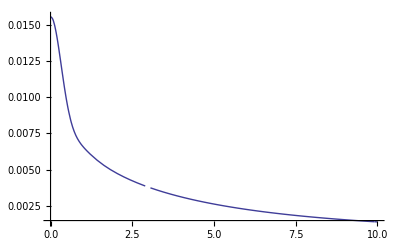

```mathematica
Plot[{fvtR1NaCllong[r]},{r,0,10},PlotRange->Full]
```

```mathematica
Export["/Users/anggao/Desktop/Na_Ca_Cl_potentials/vR1_NaCl.txt", Transpose[{Table[r,{r,0.02,20,0.02}], Table[fvtR1NaCllong[r],{r,0.02,20,0.02}]}], "Table"]
```

/Users/anggao/Desktop/Na_Ca_Cl_potentials/vR1_NaCl.txt

```mathematica
fvtR1NaCllong[0.2]
```

0.0140894

```mathematica
box=2.97
```

2.97

```mathematica
fvtR1NaCllongs[r_]:=fvtR1NaCllong[r]-Erf[r/10]/(ϵ r)
```

```mathematica
fEwaldNaCl[x_]:=Sum[Qna Qcl fvtR1NaCllongs[Sqrt[(m box-x)^2+(l box)^2+(n box)^2]],{m,-20,20},{l,-20,20},{n,-20,20}]
```

```mathematica
tableEwaldNaCl=ParallelTable[fEwaldNaCl[r],{r,0.1,1.5,0.05}]
```

{-0.156708,-0.156248,-0.155677,-0.154978,-0.154219,-0.153443,-0.152685,-0.151975,-0.151333,-0.150785,-0.150307,-0.149909,-0.149586,-0.149312,-0.149104,-0.148939,-0.148806,-0.148696,-0.148596,-0.148519,-0.148453,-0.148397,-0.148348,-0.148308,-0.148276,-0.148266,-0.148249,-0.148267,-0.148265}

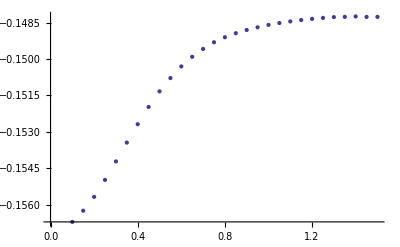

```mathematica
ListPlot[Transpose[{Table[r,{r,0.1,1.5,0.05}], tableEwaldNaCl}]]
```

```mathematica
interpEwaldNaCl=Interpolation[Transpose[{Table[r,{r,0.1,1.5,0.05}], tableEwaldNaCl}]]
```

InterpolatingFunction[{{0.1,1.5}},<>]

```mathematica
Export["/Users/anggao/Desktop/Na_Ca_Cl_potentials/VR1NaCl_Ewald.txt",Transpose[{Table[r,{r,0.1,box/2,0.001}], Table[interpEwaldNaCl[r]-interpEwaldNaCl[box/2],{r,0.1,box/2,0.001}]}],"Table"]
```

/Users/anggao/Desktop/Na_Ca_Cl_potentials/VR1NaCl_Ewald.txt

```mathematica
140*(interpEwaldNaCl[0.3]-interpEwaldNaCl[box/2])
```

-0.832618